# Crack the MJO Nut

## Slide Show Subtitle

Baoxiang Pan
2017.6.28

## Background

-Graphics-

Averages of all January–March MJO events from 1979–2016. Green shading shows below-average outgoing longwave radiation(wave length from 4 µm to 40 µm) values, indicating more clouds and rainfall, and brown shading identifies above-average OLR (drier and clearer skies than normal). The purple contours show the location and strength of the Pacific jet at the 200-hPa level (roughly 38,000 feet at that location). Note the eastward movement of the wet and dry areas. How far the Pacific jet extends past the international dateline also changes with the phase of the MJO. NOAA Climate.gov animation, adapted from original images provided by Carl Schreck.

```mathematica
GraphicsGrid[ArrayReshape[Import["/Users/lambda/Desktop/MJO.gif"],{4,2}],
Spacings->{10,-120},
ImageSize->Full]
```

-Graphics-

What is MJO

A remarkable feature of the atmospheric circulation and moist convection in the tropics is their tendency to be organized at planetary scales and to propagate eastward at an averaged speed of 5 m/s across the equatorial Indian and western/central Pacific oceans, with a local intraseasonal period of 30–90 days. This phenomenon  is known as the Madden-Julian Oscillation (MJO).

Tropical heat sources generate subtropical Rossby wave vorticity anomalies that are partially responsible for the retraction (extension) of the Pacific jet stream exit region and the formation of PNP anomalies

Wet (dry) events are favored during the phase of the oscillation associated with en- hanced convection near 150 E (120 E) in the tropical Pacific.

The life cycle of the MJO is characterized in this study in terms of variations in tropical convection and zonal component of the wind, specifically those that occur at the intraseasonal timescale.

To describe vari- ations in tropical convection, we use outgoing longwave radiation (OLR) data, which has been frequently used as a proxy for large-scale tropical convective activity (e.g., Lau and Chan 1986; Waliser et al. 1993; Jones et al. 1998).

The RMM index is a commonly used metric forthe observed and simulated/forecasted MJO.

MJO teleconnections in the northern extratropics.
Accurate predictions of MJO events are not sufficient
for successful subseasonal forecasts. The ability to
predict the impact of MJO events on the global circulation
is crucial.

The S2S database, a key component
of the World Weather Research Programme
(WWRP)/World Climate Research Programme
(WCRP) Subseasonal to Seasonal Prediction Project
science plan, is currently open to the public. It contains
reforecasts and also near-real-time subseasonal
to seasonal forecasts from all the major operational
centers.

desert of predictability

sudden stratospheric warmings

sudden stratospheric warming indices

The importance of the tropics in extra-tropical weather forecasting has been
illustrated by several authors. Early results from Ferranti et al. ( 1990 ) indicated that
better representation of the MJO led to better mid-latitude forecasts in the northern
hemisphere, and the benefi t of the connection of the MJO and NAO in intra- seasonal
forecasting has been demonstrated in Lin et al. ( 2010a ).

This type of I-know-it-when-I-see-it, but ill-defined situation is ripe for some machine learnin

The ensemble forecast is usually evaluated by comparing the average of the individual forecasts for one forecast variable to the observed value of that variable

Statistical diagnostics have led to a common perception that only few global models can reproduce the MJO. Here we demonstrate, using a method of tracking individual MJO events, that this perception is incorrect. Of 27 global model simulations diagnosed, all produced large-scale slowly eastward propagating signals in precipitation, which are taken as manifestations of the MJO. The difference is some model produced them frequently, others infrequently. There is no statistically significant distinction between the strength and propagation speeds of MJO events produced by most of these models. A hypothesis is proposed to interpret our results: A model can produce the MJO only in a particular background state. If the background state of a model can be constantly in a condition that is conducive to its production of the MJO, this model simulates the MJO frequently. If not, this model can still produce the MJO but only infrequently when its seasonal background state occasionally migrates into a condition that is conducive to its production of the MJO. Preliminary results from testing this hypothesis are presented

```mathematica
SetDirectory["/Volumes/lambda/Data/Reanalysis/NCEP/Precipitation"];
file=FileNames["*.nc"];
```

```mathematica
prate=Join[Table[Import[file[[i]],{"Datasets","prate"}],{i,Length[file]}]];
lat=Import[file[[1]],{"Datasets","lat"}];
lon=Import[file[[1]],{"Datasets","lon"}];
```

```mathematica
StormCenterDetector[pr_]:=Block[{T=20,cp},
	cp=Table[Total[pr[[i;;i+T-1,;;,;;]]],{i,1,Length[pr]-T+1,T}];
	Map[{Position[#,Max[#]][[1]],Max[#]}&,cp]];
```

```mathematica
centers=Map[StormCenterDetector[#]&,prate];
```

```mathematica
Dimensions[centers[[70]]]
```

{35,2}

```mathematica
Dimensions[test]
```

{5072,2}

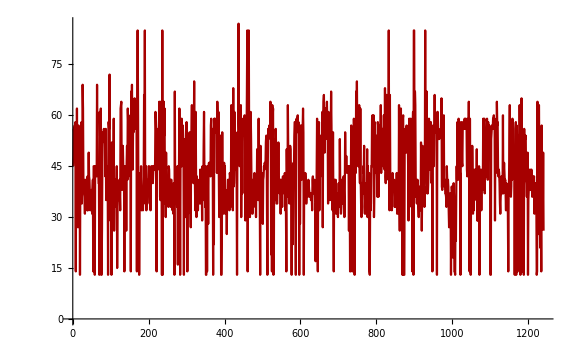

```mathematica
test=Flatten[Table[Map[#[[1,1]]&,centers[[i]]],{i,Length[file]}]];
ListLinePlot[test[[1+73*(1986-1948);;73*(2003-1948)]],PlotRange->Full,ImageSize->Large]
```

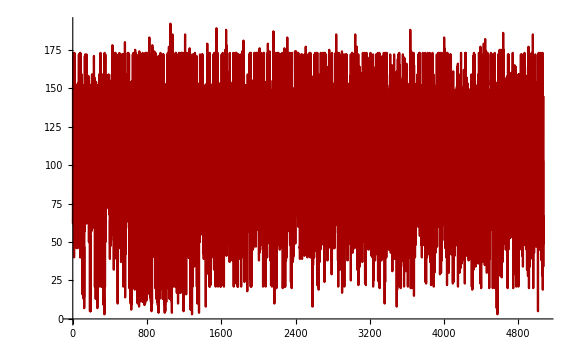

```mathematica
test=Flatten[Table[Map[#[[1,2]]&,centers[[i]]],{i,Length[file]}]];
ListLinePlot[test,PlotRange->Full,ImageSize->Large]
```

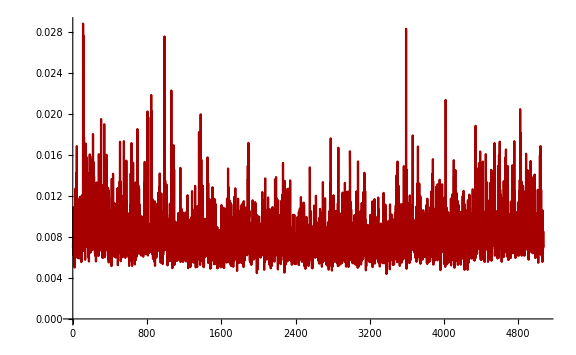

```mathematica
test=Flatten[Table[Map[#[[2]]&,centers[[i]]],{i,Length[file]}]];
ListLinePlot[test,PlotRange->Full,ImageSize->Large]
```

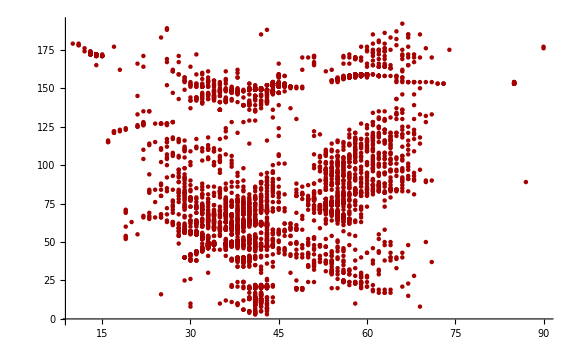

```mathematica
test=Flatten[Table[Map[{#[[1,1]],#[[1,2]]}&,centers[[i]]],{i,Length[file]}],1];
ListPlot[test,PlotRange->Full,ImageSize->Large]
```

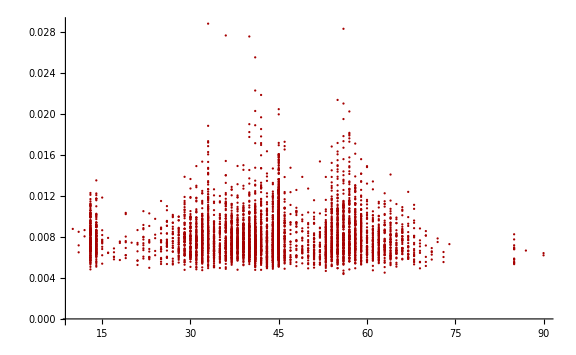

```mathematica
test=Flatten[Table[Map[{#[[1,1]],#[[2]]}&,centers[[i]]],{i,Length[file]}],1];
ListPlot[test,PlotRange->Full,ImageSize->Large]
```

```mathematica
GeoPlot[data_,bounds_]:=Block[{image},
image=ArrayPlot[data,
                 PlotRange->Full,
                 ColorFunction->Hue,
                 Frame->False,
                 PlotRangePadding->None, (* Important *)
                 PlotLegends->Automatic];
Legended[GeoGraphics[
   {{GeoStyling[{"GeoImage", image[[1]]}, 
     GeoRange -> bounds], 
     GeoBoundsRegion[bounds]},  (* image background stretched within bound area *)
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]},
    {FaceForm[],EdgeForm[Black],Polygon[LinguisticAssistant]}},
   GeoProjection ->"Mercator",
   GeoGridLines -> True, 
   GeoRange -> bounds,
   ImageSize -> Medium], 
image[[2]]]]
```